```mathematica
{a,b}={Sqrt[(x-1)^2+y^2],Sqrt[(x+1)^2+y^2]};
plt2d=ContourPlot[#,{x,-3,3},{y,-3,3},Frame->False,ColorFunction->"LightTemperatureMap",Contours-> {Automatic,25},ImageSize->360]&;
plt3d=Plot3D[#,{x,-3,3},{y,-3,3},AspectRatio->1,BoxRatios->1,ColorFunction->"TemperatureMap",Axes->False,ImageSize->360]&;
show={plt2d[#],plt3d[#]}&;
```

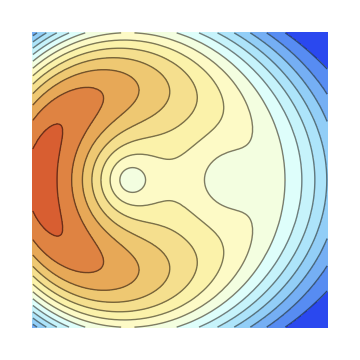
{-Graphics-,-Graphics3D-}

```mathematica
show[a Sin[b]]
```